```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S94_archive/Andrews_2016/surface diffusion

```mathematica
time=300
diffconst=100
binwidth=10
angle=ArcTan[200/150]
lowend=-450
highend=450
```

300

100

10

ArcTan[4/3]

-450

450

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
gauss[x_,mu_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)]
```

```mathematica
Assuming[s>0,Integrate[gauss[x,mu,s],{x,-Infinity,Infinity}]]
```

1

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["ribbonout.txt","CSV"];
```

```mathematica
simdata
```

{{300,509,493,604,595,698,846,872,1082,1231,1553,1823,2015,2277,2692,3171,3663,4160,4721,5366,6045,6805,7610,8214,9402,10178,11289,12247,13222,14333,15468,16854,17968,18789,20008,21009,21961,22866,23757,24617,25542,25994,26556,26818,26694,26988,27204,26901,27025,26549,25656,25350,24902,23797,22884,22024,20934,20240,18938,17498,16679,15547,14470,13402,12369,11193,10301,9308,8355,7536,6743,6112,5367,4728,4200,3636,3176,2659,2368,2043,1690,1443,1311,1101,895,859,727,597,615,544,519},{300,551,561,527,646,709,781,991,1205,1303,1464,1726,1998,2285,2801,3114,3624,4142,4800,5486,6145,6850,7523,8428,9531,10205,10994,12426,13334,14372,15752,16799,17531,18990,20129,21084,21921,22782,23979,24728,25268,25688,26394,26740,26855,27237,26913,27246,26284,26400,25917,25125,24888,23827,23342,22108,21105,20058,18888,17603,16394,15517,14479,13364,12338,11246,10121,9467,8320,7473,6775,6085,5182,4738,4190,3507,3170,2743,2388,2050,1725,1538,1252,1111,984,808,713,583,583,550,483}}

```mathematica
simdata1=Drop[simdata[[1]],1]
```

{509,493,604,595,698,846,872,1082,1231,1553,1823,2015,2277,2692,3171,3663,4160,4721,5366,6045,6805,7610,8214,9402,10178,11289,12247,13222,14333,15468,16854,17968,18789,20008,21009,21961,22866,23757,24617,25542,25994,26556,26818,26694,26988,27204,26901,27025,26549,25656,25350,24902,23797,22884,22024,20934,20240,18938,17498,16679,15547,14470,13402,12369,11193,10301,9308,8355,7536,6743,6112,5367,4728,4200,3636,3176,2659,2368,2043,1690,1443,1311,1101,895,859,727,597,615,544,519}

```mathematica
simdata2=Drop[simdata[[2]],1]
```

{551,561,527,646,709,781,991,1205,1303,1464,1726,1998,2285,2801,3114,3624,4142,4800,5486,6145,6850,7523,8428,9531,10205,10994,12426,13334,14372,15752,16799,17531,18990,20129,21084,21921,22782,23979,24728,25268,25688,26394,26740,26855,27237,26913,27246,26284,26400,25917,25125,24888,23827,23342,22108,21105,20058,18888,17603,16394,15517,14479,13364,12338,11246,10121,9467,8320,7473,6775,6085,5182,4738,4190,3507,3170,2743,2388,2050,1725,1538,1252,1111,984,808,713,583,583,550,483}

```mathematica
Length[simdata2]
```

90

```mathematica
nmolec=Total[simdata2]
Total[simdata1]
```

999980

1000000

```mathematica
xvector=Table[i,{i,lowend+binwidth/2,highend-binwidth/2,binwidth}];
```

```mathematica
Length[xvector]
```

90

```mathematica
simdata1xy=Transpose[{xvector,simdata1}];
```

```mathematica
simdata2xy=Transpose[{xvector,simdata2}];
```

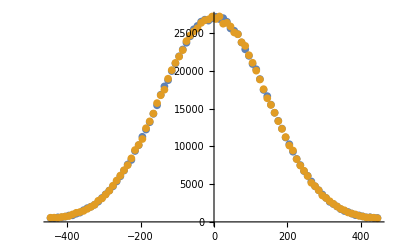

```mathematica
ListPlot[{simdata1xy,simdata2xy}]
```

```mathematica
sigma=N[Cos[angle]*Sqrt[2*time*diffconst]]
```

146.969

```mathematica
theoryfn[x_]=nmolec*binwidth*(gauss[x,0,sigma]+gauss[x,highend-lowend,sigma]+gauss[x,-(highend-lowend),sigma])
```

9999800 (0.00271446 ⅇ^(-0.0000231481 (-900+x)^2)+0.00271446 ⅇ^(-0.0000231481 x^2)+0.00271446 ⅇ^(-0.0000231481 (900+x)^2))

```mathematica
(*theoryfn[x_]=1000000*binwidth*(gauss[x,0,sigma]+gauss[x,2000,sigma]+gauss[x,-(2000),sigma])*)
```

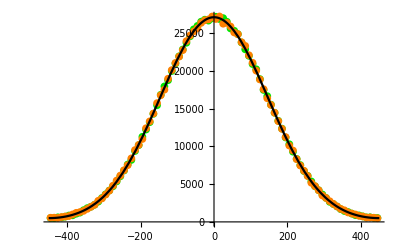

```mathematica
Show[{ListPlot[{simdata1xy,simdata2xy},PlotStyle->{RGBColor[0,0.9,0],Orange}],
Plot[theoryfn[x],{x,lowend,highend},PlotStyle->Black]},Axes->{True,False},AxesStyle->Bold,TicksStyle->Directive[FontOpacity->0,FontSize->1]]
```

```mathematica
errors1=Table[simdata1[[i]]-N[theoryfn[xvector[[i]]]],{i,1,Length[simdata1]}];
```

```mathematica
errors2=Table[simdata2[[i]]-N[theoryfn[xvector[[i]]]],{i,1,Length[simdata2]}];
```

```mathematica
StandardDeviation[errors1]
StandardDeviation[errors2]
```

102.033

124.805

```mathematica
errors1xy=Transpose[{xvector,errors1}];
```

```mathematica
errors2xy=Transpose[{xvector,errors2}];
```

```mathematica
theoryerror[x_]=Sqrt[theoryfn[x]]
```

10 √99998 √(0.00271446 ⅇ^(-0.0000231481 (-900+x)^2)+0.00271446 ⅇ^(-0.0000231481 x^2)+0.00271446 ⅇ^(-0.0000231481 (900+x)^2))

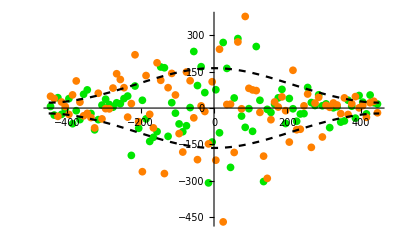

```mathematica
Show[{ListPlot[{errors1xy,errors2xy},PlotStyle->{RGBColor[0,0.9,0],Orange}],Plot[theoryerror[x],{x,lowend,highend},PlotStyle->Directive[Black,Dashed]],Plot[-theoryerror[x],{x,lowend,highend},PlotStyle->Directive[Black,Dashed]]},Axes->{True,False},AxesStyle->Bold,TicksStyle->Directive[FontOpacity->0,FontSize->1]]
```